```mathematica
Needs["VisualizeGenome`"]
Needs["BSFHistory`"]
```

```mathematica
3,9,13,16
```

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT_1DH/run_001_001_GENOMES_MATH.txt",Choice->"All"])//MatrixForm;
showAsExpressions[evo1]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]};
```

## Show GPAT Genome

```mathematica
plotAsTree[links_,nodes_,root_,leaves_,opts:OptionsPattern[]]:=
Module[{nodeSize=0.1,labels,ids},
labels=If[SyntaxQ[#[[1]]],If[
NumberQ[ToExpression[#[[1]]]],
Style[Round[ToExpression[#[[1]]],0.01],FontSize->13],
Style[#[[1]],Bold,FontSize->16]],
Style[#[[1]],Bold,FontSize->16]]&/@nodes;
If[Length[nodes[[1]]]>1,ids=nodes[[All,2]],ids=Null];
If[Length[links]>0,
TreePlot[links,Automatic,root,
VertexLabeling->True,
DirectedEdges->True,
EdgeRenderingFunction-> ({
Arrowheads->0.015,
Arrow[#1,nodeSize],
If[#3=!=None,
Inset[
Style[Text[" "<>ToString[Round[#3,0.01]]<>" "],FontSize->15],
Mean[#1],
Automatic,Automatic,
If[#1[[1,1]]<=#1[[2,1]],#1[[2]]-#1[[1]],#1[[1]]-#1[[2]]],
Background->White]
]
}&),
VertexRenderingFunction->({
RGBColor[0.313,0.555,1],
EdgeForm[Directive[Black,Thick]],
If[MemberQ[leaves,#2],
RGBColor[1,0.5,0.078]
],
If[#2==root,
RGBColor[1,0.188,0.188]
],
Disk[#1,nodeSize],
Black,
Inset[Text[labels[[#2]]],#1],
If[ids=!=Null,Inset[Text[ids[[#2]]],#1-{nodeSize*1.7,0}]]
}&),
ImagePadding->40,
Sequence@@FilterRules[{opts}, Options[TreePlot]]
],
(* single node only *)
Graphics[{
RGBColor[1,0.188,0.188],
EdgeForm[Directive[Black,Thick]],
Disk[{0,0},nodeSize],
Black,
Inset[Text[labels[[1]]],{0,0}],
If[ids=!=Null,Inset[Text[ids[[1]]],{-nodeSize*1.7,0}]]
}]
]
]
```

```mathematica
convertAndPlotGP[tree_]:=
Module[{root,depth,nodeIds,links, nodes,order,rename,weights,linksW,tgraph,coords,range,minMax,leaves},
root=ROOT/.tree;
depth=DEPTH/.tree;
links=(LINKS/.tree)[[All,1]];
nodeIds=(NODES/.tree)[[All,1]];
order=Join[{root},Select[nodeIds,#≠root&]];
rename=Thread[Rule[order,Range[Length[nodeIds]]]];
root=root/.rename;
links=links/.rename;
nodeIds=nodeIds/.rename;
nodes=Sort[{#[[1]]/.rename,Sequence@@#[[2;;-1]]}&/@(NODES/.tree),#1[[1]]<#2[[1]]&];

leaves=Complement[nodeIds, links[[All,2]]];
nodes=nodes[[All,2;;3]]/.{"plus"->"+","add"->"+","times"->"*","gauss"->"G","atan"->"A","sin"->"S"};
weights=If[#[[3]],#[[2]],1]&/@(LINKS/.tree);
linksW=If[#[[2]]==1,#[[1]],#]&/@Thread[{links,weights}];

tgraph=plotAsTree[linksW,nodes,root,leaves];
coords=Extract[tgraph,#[[1;;-2]]~Join~{1}]&/@Position[tgraph,Disk];
minMax=Transpose[{Min/@Transpose[coords],Max/@Transpose[coords]}];
range=Abs[#[[1]]-#[[2]]]&/@minMax;

plotAsTree[linksW,nodes,root,leaves,
PlotRange->minMax,
AspectRatio->If[range[[1]]>0,range[[2]]/range[[1]],depth/2],
ImageSize->{400,400}]
]
```

```mathematica
graphs=Transpose[{Range[7,8],(convertAndPlotGP[#]&/@evo1[[7;;8,4,1]])}];
graphs=DeleteDuplicates[graphs,#1[[2]]==#2[[2]]&];
```

1

{{S,7},{+,2}}

1

{{S,7},{+,2},{1,0}}

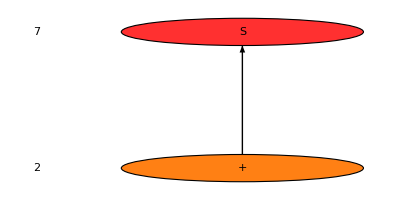
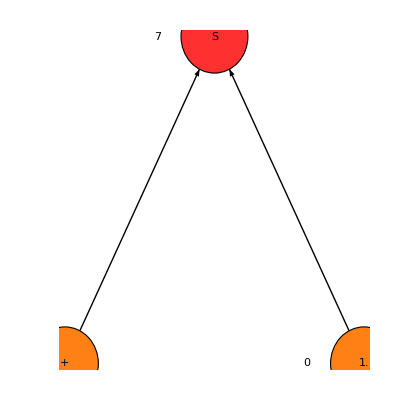
7 | -Graphics-
8 | -Graphics-

```mathematica
Grid[graphs,Frame->All]
```

```mathematica
evo1[[7;;8]]
```

{{7,603,501,{{NODES→{{0,sin,7},{1,plus,2}},LINKS→{{1→0,-2.91843,False}},ROOT→0,DEPTH→1}},0.0394173},{8,792,603,{{NODES→{{0,sin,7},{1,plus,2},{2,1,0}},LINKS→{{1→0,-2.91843,False},{2→0,1.,False}},ROOT→0,DEPTH→1}},0.0503086}}

```mathematica
sel1=Select[evo1,MemberQ[{2,10},#[[1]]]&]
```

{{2,179,1,{{NODES→{{0,plus},{1,x0}},LINKS→{{1→0,0.606775,True}},ROOT→0,DEPTH→1}},0.0257477},{10,938,860,{{NODES→{{0,plus},{1,gauss},{2,1}},LINKS→{{2→1,-0.74163,False},{1→0,2.27239,True}},ROOT→0,DEPTH→2}},0.0502294}}

```mathematica
sel1[[1;;2,4,1]]
```

{{NODES→{{0,plus},{1,x0}},LINKS→{{1→0,0.606775,True}},ROOT→0,DEPTH→1},{NODES→{{0,plus},{1,gauss},{2,1}},LINKS→{{2→1,-0.74163,False},{1→0,2.27239,True}},ROOT→0,DEPTH→2}}

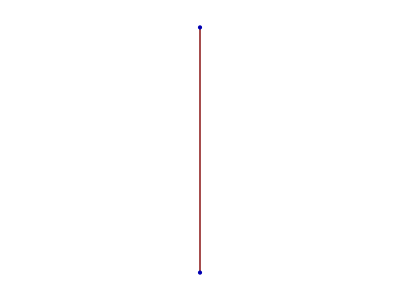

```mathematica
TreePlot[{1->2}]
```